```mathematica
h[s_]:=Evaluate[Integrate[Sqrt[1/Sqrt[1-t^2]]*Exp[-I*t*s],{t,-1,1}]]
```

```mathematica
h[s]
```

√π Gamma[3/4] Hypergeometric0F1Regularized[5/4,-s^2/4]

```mathematica
Simplify[h[s]]
```

√π Gamma[3/4] Hypergeometric0F1Regularized[5/4,-s^2/4]

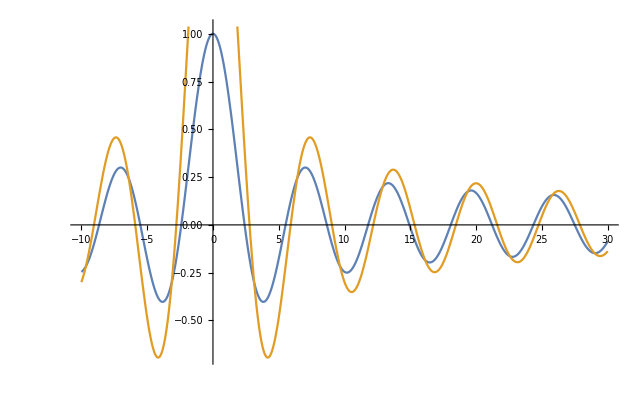

```mathematica
Plot[{BesselJ[0,s],h[s]},{s,-10,30}]
```